# Rebuttal figures

Rebuttal versions of the paper's figures, in the style of ai_plots.nb. Run the Setup cell first; every other section is independent. Inputs: data/ next to this notebook (rebuild with prepare_data.py); outputs: pdf/. Section comments say what changed relative to the paper.

## Setup (run first)

```mathematica
(* Rebuttal versions of the paper figures. Each section follows the matching cell of ai_plots.nb;
   inputs are in data/ next to this notebook (made by prepare_data.py), PDFs go to pdf/. *)
If[! StringQ[figDir], figDir = NotebookDirectory[]];
data = FileNameJoin[{figDir, "data"}];
out = If[StringQ[figOut], figOut, FileNameJoin[{figDir, "pdf"}]];   (* figOut: optional other output folder *)
If[! DirectoryQ[out], CreateDirectory[out]];
readCSV[f_] := Module[{t = Import[FileNameJoin[{data, f}], "CSV"]}, AssociationThread[First[t], #] & /@ Rest[t]];
row1[rows_, crit_] := First[Select[rows, crit]];
runs[mask_] := Select[Split[Range[Length[mask]], mask[[#1]] === mask[[#2]] &], mask[[First[#]]] && Length[#] > 1 &];
models = {"mistrallarge123b", "glm45air", "qwen235b", "qwen32b", "llama33_70b", "mixtral8x22b", "gptoss120b", "gptoss120b_harmony"};
mmodels = {"Mistral Large 2", "GLM-4.5-Air", "Qwen3-235B", "Qwen3-32B", "Llama-3.3-70B", "Mixtral-8x22B", "gpt-oss-120b", Row[{"gpt-oss-120", Superscript["b", "*"]}]};
cols = {{1, 0, 0}, {0.9, 0.5, 0}, {0.8, 0.8, 0}, {0, 0.75, 0}, {0, 0.6, 0.8}, {0.5, 0, 0.6}, {0.5, 0.5, 0.5}};
bandOpacity = 0.18;   (* 5-95% bands over the 100 splits *)
nullGray = GrayLevel[0.55]; nullOpacity = 0.22;   (* permutation null of the angle *)
```

## Figure 2: decodability across normalized depth (80/20 splits, PCA fitted on training objects)

```mathematica
k2 = 8;
minR2band = 0.05;   (* bands are drawn only where the median R^2 exceeds this, to keep early layers readable *)
S2 = Table[readCSV["split/" <> m <> "_split_r2_" <> ToString[k2] <> ".csv"], {m, models[[1 ;; 7]]}];
N2 = Table[readCSV["null/k8/" <> m <> "_angle_null.csv"], {m, models[[1 ;; 7]]}];
w = 2; x2[la_, l_] := w*(la - 1)/(l - 1);
yR[v_] := Clip[v, {0, 1}]; yA[v_] := Clip[1 - v/90, {0, 1}];
band2[s_, f_, lo_, hi_] := Module[{t = S2[[s]], l = Length[S2[[s]]], mask},
   mask = (#["r2"] > minR2band) & /@ t;
   {Opacity[bandOpacity], RGBColor @@ cols[[s]], EdgeForm[],
    Table[Polygon[Join[Table[{x2[la, l], f[t[[la, lo]]]}, {la, r}], Table[{x2[la, l], f[t[[la, hi]]]}, {la, Reverse[r]}]]], {r, runs[mask]}]}];
(* null averaged over the 7 models at the same normalized depth *)
nullAt[key_] := Table[Mean[Table[Interpolation[Table[{(la - 1)/(Length[N2[[s]]] - 1), N2[[s, la, key]]}, {la, Length[N2[[s]]]}], InterpolationOrder -> 1][u], {s, 7}]], {u, 0, 1, 0.01}];
nul2 = {nullAt["null_ang_p05"], nullAt["null_ang_p50"], nullAt["null_ang_p95"]};
panel2[f_, c_, lo_, hi_, labs_, extra_] := Graphics[{
    Thickness[0.001], Table[{GrayLevel[0.75], Line[{{w - 1.3 + i/30, i/10}, {w, i/10}}]}, {i, 1, 9}],
    extra,
    Table[band2[s, f, lo, hi], {s, 7, 1, -1}],
    Thickness[0.004], Opacity[1],
    Table[{RGBColor @@ cols[[s]], Line[Table[{x2[la, Length[S2[[s]]]], f[S2[[s, la, c]]]}, {la, 1, Length[S2[[s]]]}]],
      Text[Style[mmodels[[s]], 13], {0.4, 1.05 - s/7.7}]}, {s, 7, 1, -1}],
    Black, Thickness[0.001], Line[{{0, 0}, {0, 1}, {w, 1}, {w, 0}, {0, 0}}], labs}, ImageSize -> 420];
nullBand2 = {nullGray, Opacity[nullOpacity], EdgeForm[],
   Polygon[Join[Table[{w*(i - 1)/100, yA[nul2[[1, i]]]}, {i, 101}], Table[{w*(i - 1)/100, yA[nul2[[3, i]]]}, {i, 101, 1, -1}]]],
   Opacity[1], Dashing[{0.01, 0.01}], Thickness[0.002], Line[Table[{w*(i - 1)/100, yA[nul2[[2, i]]]}, {i, 101}]], Dashing[None]};
fig2r = panel2[yR, "r2", "r2_p05", "r2_p95",
   Table[{Black, Text[i/10., {w + 0.1, i/10}], Line[{{w, i/10}, {w + 0.02, i/10}}]}, {i, 0, 10}], {}];
fig2a = panel2[yA, "ang", "ang_p05", "ang_p95",
   Table[{Black, Text[10*i, {w + 0.1, 1 - i/9}], Line[{{w, 1 - i/9}, {w + 0.02, 1 - i/9}}]}, {i, 0, 9}], nullBand2];
Export[FileNameJoin[{out, "fig2_r2.pdf"}], fig2r]; Export[FileNameJoin[{out, "fig2_ang.pdf"}], fig2a];
GraphicsRow[{fig2r, fig2a}, ImageSize -> 900]
```

## Figures 3 and 12: per-model R^2 (black) and angle (gray) with the PCA strips

```mathematica
(* thick: top-4 (top-16 for gpt-oss), thin: top-8 (top-32); thin curves carry 5-95% bands over splits;
   dashed gray: median angle under shuffled sky labels (same k as the thin curve), with its 5-95% band *)
lss = {39, 24, 82, 50, 37, 23, 22, 22};
dumpChart[sample_] := Module[{model = models[[sample]], gpt = sample >= 7, kA, kB, brk, A, B, NL, P1, P2, P3, pic, l, w = 3, s = 0.5, x, wcord, scord,
    th1 = 0.004, th2 = 0.002, ls = lss[[sample]], nk, ab},
   {kA, kB} = If[gpt, {16, 32}, {4, 8}]; brk = If[gpt, 32, 8];
   P1 = Import[FileNameJoin[{data, "strips", model <> "_sky_cov_scaled_128.csv"}]]; P1 = Transpose[P1[[2 ;;]]][[3 ;; 130]];
   P2 = Import[FileNameJoin[{data, "strips", model <> "_sky_cov_equal_128.csv"}]]; P2 = Transpose[P2[[2 ;;]]][[3 ;; 130]];
   P3 = Import[FileNameJoin[{data, "strips", model <> "_type_cov_equal_128.csv"}]]; P3 = Transpose[P3[[2 ;;]]][[3 ;; 130]];
   pic = Transpose[{P1, P2, P3}, {3, 1, 2}];
   A = readCSV["split/" <> model <> "_split_r2_" <> ToString[kA] <> ".csv"];
   B = readCSV["split/" <> model <> "_split_r2_" <> ToString[kB] <> ".csv"];
   nk = If[FileExistsQ[FileNameJoin[{data, "null", "k" <> ToString[kB], model <> "_angle_null.csv"}]], kB, 8];
   NL = readCSV["null/k" <> ToString[nk] <> "/" <> model <> "_angle_null.csv"];
   l = Length[B];
   x[la_] := w*((la - 0.5)/l);
   wcord[{p_, la_}] := {x[la], (-s)*(p/brk)};
   scord[{p_, la_}] := {x[la], -s - ((p - brk)/(128 - brk))*(1 - s)};
   ab[t_, lo_, hi_, f_] := Polygon[Join[Table[{x[i], f[t[[i, lo]]]}, {i, l}], Table[{x[i], f[t[[i, hi]]]}, {i, l, 1, -1}]]];
   Graphics[{EdgeForm[],
     Table[{RGBColor @@ (1 - Sqrt[#1] &) /@ pic[[p, la]], Polygon[(wcord[{p, la} - #1] &) /@ ({{0, -1}, {0, 1}, {2, 1}, {2, -1}}/2)]}, {p, 1, brk}, {la, 1, l}],
     Table[{RGBColor @@ (1 - Sqrt[#1] &) /@ pic[[p, la]], Polygon[(scord[{p, la} - #1] &) /@ ({{0, -1}, {0, 1}, {2, 1}, {2, -1}}/2)]}, {p, brk + 1, 128}, {la, 1, l}],
     (* null of the angle *)
     nullGray, Opacity[nullOpacity], ab[NL, "null_ang_p05", "null_ang_p95", Clip[1 - #/90, {0, 1}] &], Opacity[1],
     Dashing[{0.008, 0.008}], Thickness[th2], Line[Table[{x[i], Clip[1 - NL[[i, "null_ang_p50"]]/90, {0, 1}]}, {i, l}]], Dashing[None],
     (* bands of the thin curves *)
     GrayLevel[0.75], Opacity[0.3], ab[B, "ang_p05", "ang_p95", Clip[1 - #/90, {0, 1}] &],
     Black, Opacity[0.12], ab[B, "r2_p05", "r2_p95", Clip[#, {0, 1}] &], Opacity[1],
     Thickness[th1], GrayLevel[0.75], Line[Table[{x[i], 1 - A[[i, "ang"]]/90}, {i, 1, l}]],
     Thickness[th2], Line[Table[{x[i], 1 - B[[i, "ang"]]/90}, {i, 1, l}]],
     Black, Thickness[th1], Line[Table[{x[i], Max[A[[i, "r2"]], 0]}, {i, 1, l}]],
     Thickness[th2], Line[Table[{x[i], Max[B[[i, "r2"]], 0]}, {i, 1, l}]],
     Dashing[None], Thickness[0.001], Line[{{w, 1}, {w, -1}, {0, -1}, {0, 1}, {w, 1}, {w, 0}, {0, 0}}],
     Table[{Text[10*i, {x[10*i + 1], 1.1}], Line[{{x[10*i + 1], 1.07}, {x[10*i + 1], 1}}], Text[10*i, {x[10*i + 1], -1.1}], Line[{{x[10*i + 1], -1.07}, {x[10*i + 1], -1}}]}, {i, 0, Floor[l/10]}],
     Table[{Line[{{x[i + 1], 1.03}, {x[i + 1], 1}}], Line[{{x[i + 1], -1.03}, {x[i + 1], -1}}]}, {i, 1, l - 1}],
     Table[{Line[{{x[5*i + 1], 1.06}, {x[5*i + 1], 1}}], Line[{{x[5*i + 1], -1.06}, {x[5*i + 1], -1}}]}, {i, 1, Floor[(l - 1)/5]}],
     Table[{Line[{{-0.05, i}, {0, i}}]}, {i, 0, 1, 0.1}],
     Table[{Text[i, {-0.12, i + 0.02}], Line[{{-0.08, i}, {0, i}}]}, {i, 0, 1}],
     Text[Style[Superscript["R", 2], 15], {-0.15, 0.5}], Text[Style["layer", 15], {w/2, -1.25}], Text[Style[mmodels[[sample]], 16], {w/4, 0.75}],
     Gray, Table[{Text[10*i, {w + 0.1, 1 - i/9}], Line[{{w, 1 - i/9}, {w + 0.02, 1 - i/9}}]}, {i, 0, 9, 1}], Text[Style["α", 15], {w + 0.25, 0.5}], Black,
     Line[{{{x[ls + 1], -s/2}, {w + 0.02, -s/2}}, {{x[ls + 1], -s}, {w + 0.02, -s}}, {{w, -1}, {w + 0.02, -1}}}],
     Text[brk, {w + 0.1, -s}, Automatic, {0, -1}], Text[brk/2, {w + 0.1, -s/2}, Automatic, {0, -1}], Text[128, {w + 0.1, -1}, Automatic, {0, -1}],
     Text[Style["PCA", 15], {w + 0.1, -0.75}, Automatic, {0, -1}]}, ImageSize -> 420]];
dumps = Table[dumpChart[i], {i, 1, 8}];
Do[Export[FileNameJoin[{out, models[[i]] <> "_dump.pdf"}], dumps[[i]]], {i, 1, 8}];
GraphicsGrid[Partition[dumps, 2], ImageSize -> 900]
```

## Figures 5 and 16: ablation, with 95% intervals and the shuffled-answer baseline

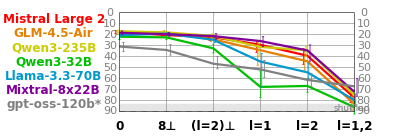

```mathematica
(* models are picked by name (the paper's cell had Qwen3-235B and Qwen3-32B swapped);
   intervals resample query objects (rebuttal/intervals.py); gray band at the bottom: the median
   separation when query objects are shuffled against each model's answers, 5-95% over shuffles *)
AB = readCSV["ablation/ablation_intervals.csv"]; BL = readCSV["ablation/baseline_angle.csv"];
abModels = {"mistrallarge123b", "glm45air", "qwen235b", "qwen32b", "llama33_70b", "mixtral8x22b", "gptoss120b_harmony"};
abNames = {"Mistral Large 2", "GLM-4.5-Air", "Qwen3-235B", "Qwen3-32B", "Llama-3.3-70B", "Mixtral-8x22B", "gpt-oss-120b*"};
conds = {"none", "comp8", "l2pure", "sky3", "l2raw", "harm8"}; reg = {"0", "8⊥", "(l=2)⊥", "l=1", "l=2", "l=1,2"};
ab[m_, c_] := row1[AB, #model === m && #condition === c &];
shuf = Select[BL, #baseline === "answers_shuffled" && MemberQ[abModels, #model] &];
shufLo = Min[#["p05"] & /@ shuf]; shufHi = Max[#["p95"] & /@ shuf]; shufMed = Mean[#["median_deg"] & /@ shuf];
cap = 0.012; dxm = 0.014;
figAbl = Graphics[{Thickness[0.001], Gray, Table[Line[{{0, i/9}, {2.5, i/9}}], {i, 1, 8}], Table[Line[{{i/2, 0}, {i/2, 1}}], {i, 1, 4}],
    nullGray, Opacity[nullOpacity], EdgeForm[], Polygon[{{0, 0}, {2.5, 0}, {2.5, Clip[1 - shufLo/90, {0, 1}]}, {0, Clip[1 - shufLo/90, {0, 1}]}}], Opacity[1],
    Dashing[{0.01, 0.01}], Line[{{0, Clip[1 - shufMed/90, {0, 1}]}, {2.5, Clip[1 - shufMed/90, {0, 1}]}}], Dashing[None],
    Table[With[{m = abModels[[j]], d = (j - 4)*dxm}, {RGBColor @@ cols[[j]], Text[Style[abNames[[j]], 12, Bold], {-0.7, 1 - (j - 0.5)/7}],
       Thickness[0.004], Line[Table[{(k - 1)/2, 1 - ab[m, conds[[k]]]["median_deg"]/90}, {k, 1, 6}]],
       Thickness[0.0015], Table[With[{r = ab[m, conds[[k]]], xx = (k - 1)/2 + d},
         {Line[{{xx, 1 - r["ci95_lo"]/90}, {xx, 1 - r["ci95_hi"]/90}}], Line[{{xx - cap, 1 - r["ci95_lo"]/90}, {xx + cap, 1 - r["ci95_lo"]/90}}],
          Line[{{xx - cap, 1 - r["ci95_hi"]/90}, {xx + cap, 1 - r["ci95_hi"]/90}}]}], {k, 1, 6}]}], {j, 1, 7}],
    Black, Thickness[0.001], Line[{{0, 0}, {0, 1}, {2.5, 1}, {2.5, 0}, {0, 0}}],
    Gray, Table[{Text[10*i, {-0.1, 1 - i/9}], Text[10*i, {2.6, 1 - i/9}]}, {i, 0, 9}],
    Text[Style["shuffled", 9], {2.47, 0.035}, {1, 0}],
    Black, Table[Text[Style[reg[[i]], Bold, 12], {(i - 1)/2, -0.15}], {i, 1, 6}]}, ImageSize -> 400];
(*Export[FileNameJoin[{out, "ablation.pdf"}], figAbl];*)
figAbl
```

## Figure 17: fraction of usable responses (legend fixed)

```mathematica
AS = readCSV["ablation/all_models_summary.csv"];
condRow[m_, c_] := row1[AS, #model === m && #condition === c &];
figParsed = Graphics[{Thickness[0.001], Gray, Table[Line[{{0, i/10}, {2.5, i/10}}], {i, 1, 9}], Table[Line[{{i/2, 0}, {i/2, 1}}], {i, 1, 4}], Thickness[0.004],
    Table[With[{m = abModels[[j]]}, {RGBColor @@ cols[[j]], Text[Style[abNames[[j]], 12, Bold], {-0.7, 1 - (j - 0.5)/7}],
       Line[Table[{(k - 1)/2, condRow[m, conds[[k]]]["frac_parsed"] + condRow[m, conds[[k]]]["frac_options"]}, {k, 1, 6}]]}], {j, 1, 7}],
    Black, Thickness[0.001], Line[{{0, 0}, {0, 1}, {2.5, 1}, {2.5, 0}, {0, 0}}], Gray,
    Table[{Text[0.1*i, {-0.1, i/10}], Text[0.1*i, {2.6, i/10}]}, {i, 0, 10}], Black,
    Table[Text[Style[reg[[i]], Bold, 12], {(i - 1)/2, -0.15}], {i, 1, 6}]}, ImageSize -> 400];
Export[FileNameJoin[{out, "ablation_parsed.pdf"}], figParsed];
figParsed
```

## Figures 7 and 18: steering, map refitted without A and B

```mathematica
(* columns per model: no intervention, towards A (l=1; l=1,2), towards B (l=1; l=1,2).
   Each column is split into one sub-column per evaluation template (0 and 18 as published, plus the
   three of steering_templates_extra.csv), at the same total width. Within a column the templates are
   sorted, highest first, by ramble A + A + <30 A (A and no-intervention columns) or by ramble A + A +
   <30 A + other (B columns), so the spread of that edge
   across templates is the uncertainty. The thin lines join the pooled (mean over templates) edges.
   steeringFig[paperGet] redraws the published version (two templates pooled, one bar per column). *)
steerOrder = {"mistrallarge123b", "glm45air", "qwen235b", "qwen32b", "llama33_70b", "mixtral8x22b"};
subGap = 0.15;         (* white gap between template sub-columns, as a fraction of their width *)
sortDescending = True;  (* False: lowest sum first *)
showPooled = True;     (* thin lines at the pooled edges *)
TT = readCSV["steering/steering_templates.csv"];
toSt[r_] := {r["model"], r["arm"], r["n"], "rich", r["no_constellation"], r["ramble_A"], r["equals_A"], r["equals_B"],
   r["within30_A_not_A"], r["within30_B_not_B"], r["other"]};   (* the column layout of all_models_summary_rich.csv *)
(* sort key: ramble A + A + <30 A in the A and no-intervention columns; the same plus "other" in the B columns *)
sortKey[arm_] := If[arm === "target", #["ramble_A"] + #["equals_A"] + #["within30_A_not_A"] + #["other"] &,
    #["ramble_A"] + #["equals_A"] + #["within30_A_not_A"] &];
templateGet[m_, modes_, arm_] := Module[{s = SortBy[Select[TT, #model === m && #modes === modes && #arm === arm &], sortKey[arm]]},
    toSt /@ If[sortDescending, Reverse[s], s]];
paperT = Import[FileNameJoin[{data, "steering", "paper_l12.csv"}]][[2 ;; 19]];
paperT2 = Import[FileNameJoin[{data, "steering", "paper_l1.csv"}]][[2 ;; 19]];
paperGet[m_, modes_, arm_] := {First[Select[If[modes === "l=1", paperT2, paperT], #[[1]] === m && #[[2]] === arm &]][[1 ;; 11]]};
pooled[sts_] := Join[sts[[1, 1 ;; 4]], Mean[sts[[All, 5 ;; 11]]]];
steeringFig[get_] := Module[{v = 0.175, w, cs, bar, column, edges, line, names, cols},
   w = v*0.7;
   cs = {Red, Orange, Yellow, GrayLevel[0.73], RGBColor[0, 0.65, 0.65], Blue, White};
   (* segment edges of a bar from the top: 1, top of B, top of <30 B, top of other, top of <30 A, top of ramble A, top of A, 0 *)
   edges[st_] := {1, Total[st[[6 ;; 11]]], st[[6]] + st[[7]] + st[[9]] + st[[10]] + st[[11]], st[[6]] + st[[7]] + st[[9]] + st[[11]],
      st[[6]] + st[[7]] + st[[9]], st[[6]] + st[[7]], st[[7]], 0};
   (* stacked bar of one summary row st at x with width wd: A, ramble A, <30 A, other, <30 B, B from the bottom; unparsed from the top *)
   bar[st_, x_, wd_] := {White, Parallelogram[{x, 1}, {{wd, 0}, {0, -st[[5]]}}], Blue, Parallelogram[{x, st[[7]] + st[[9]] + st[[11]] + st[[10]] + st[[6]]}, {{wd, 0}, {0, st[[8]]}}], cs[[5]],
     Parallelogram[{x, st[[7]] + st[[9]] + st[[11]] + st[[6]]}, {{wd, 0}, {0, st[[10]]}}], cs[[4]], Parallelogram[{x, st[[7]] + st[[9]] + st[[6]]}, {{wd, 0}, {0, st[[11]]}}], Yellow,
     Parallelogram[{x, st[[7]] + st[[6]]}, {{wd, 0}, {0, st[[9]]}}], Orange, Parallelogram[{x, st[[7]]}, {{wd, 0}, {0, st[[6]]}}], Red, Parallelogram[{x, 0}, {{wd, 0}, {0, st[[7]]}}]};
   (* one column of total width w, split into one sub-column per template *)
   column[sts_, x_] := With[{n = Length[sts], ws = w/Length[sts]},
     Table[bar[sts[[k]], x + (k - 1)*ws + If[n > 1, subGap*ws/2, 0], If[n > 1, (1 - subGap)*ws, ws]], {k, n}]];
   line[sts_, x_] := With[{h = Transpose[edges /@ (pooled /@ sts)]},
     Line[Table[Catenate[Table[{{x + (i - 1)*v, h[[j, i]]}, {x + (i - 1)*v + w, h[[j, i]]}}, {i, 1, 5}]], {j, 1, 8}]]];
   cols[m_] := {get[m, "l=1,2", "untouched"], get[m, "l=1", "self"], get[m, "l=1,2", "self"], get[m, "l=1", "target"], get[m, "l=1,2", "target"]};
   names = {"A", "ramble A", "<30° A", "other", "<30° B", "B", "unparsed"};
   Graphics[{Table[With[{m = steerOrder[[j]], c = cols[steerOrder[[j]]]}, {Text[Style[m, Bold], {j + 2*v + w/2, 1.15}],
        Table[column[c[[i]], j + (i - 1)*v], {i, 5}],
        If[showPooled || Max[Length /@ c] == 1, {Black, Thickness[0.001], line[c, j]}, {}],
        Text[Style["1", 9], {j + v + w/2, -0.23}], Text[Style["1,2", 8], {j + 2*v + w/2, -0.23}], Text[Style["1", 9], {j + 3*v + w/2, -0.23}],
        Text[Style["1,2", 8], {j + 4*v + w/2, -0.23}], Text[Style["A", Bold, Red], {j + v + w/2, -0.08}], Text[Style["A", Bold, Red], {j + 2*v + w/2, -0.08}],
        Text[Style["B", Bold, Blue], {j + 3*v + w/2, -0.08}], Text[Style["B", Bold, Blue], {j + 4*v + w/2, -0.08}]}], {j, 1, 6}],
     EdgeForm[{Thickness[0.001], Black}],
     Table[{cs[[i]], Parallelogram[{0, 0.1 + (i - 1)/7}, {{0.6, 0}, {0, 1/7}}], If[i == 6 || i == 1, White, Black], Text[Style[names[[i]], Bold], {0.3, 0.1 + (i - 0.5)/7}]}, {i, 1, 7}],
     Text[Style["steer towards:", 12], {0.4, -0.08}], Text[Style["modes used:", 12], {0.4, -0.25}]}, ImageSize -> 650]];
figSteer = steeringFig[templateGet];
Export[FileNameJoin[{out, "steering.pdf"}], figSteer];
Export[FileNameJoin[{out, "steering_paper_fit.pdf"}], steeringFig[paperGet]];
figSteer
```

## Figures 8 and 19: sphere vs cylinder vs flat chart, with held-out gains

```mathematica
(* ====Figures 8 and 19:sphere vs cylinder vs flat chart,three separate figures====*)(*All three from one run:188 objects (85 stars,15 other,88 constellations as points at their area centroids);per split/resample,per-feature standardization,centring of each type on its own mean and the top-8 PCA are fitted in the full hidden space on the training (or drawn) rows (rebuttal/metric_fullpca_cent.py on the raw activations);one RA cut and one cylinder frame per model,chosen by the all-layer mean held-out R^2 of the rival alone (printed in each panel;rebuttal/metric_fullpca_allscore.py+metric_gain_typed.py).vs_original_choice_full.pdf:the paper's OLS on the squared-distance RDM,design sphere (x,y,z)+chart (lat,lon-cut)+cylinder (sin lat,cos lon,sin lon) (=the paper's seven coordinates at cut 0,equatorial);
green thick:sphere (y,z),red:cylinder (cos lon,sin lon),blue:chart (lon-cut).Band:5-95% over 100 object-bootstrap resamples within type,everything refitted per resample (metric_fullpca_score.py--ols-only).vs_chart_linmap_full.pdf/vs_cylinder_linmap_full.pdf:held-out R^2 gain from adding one map's coordinates to the other's,ridge linear map coordinates->8 PCs (cross terms included).Solid+band:median and 5-95% over 100 object splits (20% of each type held out;scored on pairs with a test object).Green:sphere added to the rival;blue/red:chart/cylinder added to the sphere.Thin lines (vsEnvelope=True):sensitivity to the coordinate choice,the lowest and highest value at each layer over all choices (OLS:3 chart frames x 12 cuts x 3 cylinder frames;linmap:chart 3 frames x 12 cuts,cylinder 3 frames;median over splits per choice).Per-model PDFs: <model>_vs_original_choice_full.pdf, <model>_vs_chart_linmap_full.pdf, <model>_vs_cylinder_linmap_full.pdf*)vsModels = Range[6]; vsEnvelope = True;
vsW = 3; vsTh = 0.004; vsGreen = RGBColor[0, 0.75, 0]; vsRed = RGBColor[1, 0, 0]; vsBlue = RGBColor[0, 0, 1];
vsX[l_][la_] := vsW*((la - 0.5)/l);
vsFrame[l_, ylo_, yhi_] := {Black, Thickness[0.001], Line[{{0, ylo}, {vsW, ylo}, {vsW, yhi}, {0, yhi}, {0, ylo}}], Table[With[{h = Which[Mod[i, 10] == 0, 0.07, Mod[i, 5] == 0, 0.06, True, 0.03]}, {Line[{{vsX[l][i + 1], ylo}, {vsX[l][i + 1], ylo - h}}], Line[{{vsX[l][i + 1], yhi}, {vsX[l][i + 1], yhi + h}}]}], {i, 0, l - 1}], Table[Text[10*i, {vsX[l][10*i + 1], ylo - 0.17}], {i, 0, Floor[(l - 1)/10]}], Text[Style["layer", 15], {vsW/2, ylo - 0.36}]};
vsYTicks[ticks_] := {Black, Thickness[0.001], Table[{Line[{{vsW, t[[1]]}, {vsW + 0.08, t[[1]]}}], Text[t[[2]], {vsW + 0.17, t[[1]]}]}, {t, ticks}]};
(*one curve:{color,thickness,layers (1-based),values,lo,hi},values already in plot units*)
vsCurve[{c_, th_, ls_, v_, lo_, hi_}, l_, {ylo_, yhi_}] := Module[{cl = Clip[#, {ylo, yhi}] &}, {{EdgeForm[], c, Opacity[bandOpacity], Polygon[Join[Transpose[{vsX[l] /@ ls, cl /@ lo}], Reverse[Transpose[{vsX[l] /@ ls, cl /@ hi}]]]]}, {c, Thickness[th], Line[Transpose[{vsX[l] /@ ls, cl /@ v}]]}}];
vsCutNote[cuts_] := If[Length[Union[cuts]] == 1, "cut: " <> ToString[First[cuts]] <> "°", "cut: per layer"];
(*panel notes,top left:model,then the coordinate choices;y in plot units*)
vsNotes[i_, lines_, {y0_, dy_}] := {Text[Style[mmodels[[i]], 16], {vsW/4, y0}], Table[Text[Style[lines[[k]], 12], {vsW/4, y0 - k*dy}], {k, Length[lines]}]};

(*OLS weights (Sum beta) on[sMin,sMax];plotted at half scale as in the paper,tick labels in Sum beta*)
vsOls[i_, {sMin_, sMax_}] := Module[{T = readCSV["vs/" <> models[[i]] <> "_vs_choice_full.csv"], l, ls, s, lo = sMin/2, hi = sMax/2}, l = Length[T]; ls = (#["layer"] + 1) & /@ T;
   s[k_] := Table[(#[k <> suf]/2) & /@ T, {suf, {"", "_p05", "_p95"}}];
   Graphics[{GrayLevel[0.5], Thickness[0.001], Line[{{0, 0}, {vsW, 0}}], vsCurve[{vsRed, vsTh, ls, Sequence @@ s["cylinder"]}, l, {lo, hi}], vsCurve[{vsBlue, vsTh, ls, Sequence @@ s["chart"]}, l, {lo, hi}], vsCurve[{vsGreen, 2*vsTh, ls, Sequence @@ s["sphere"]}, l, {lo, hi}], If[vsEnvelope, Table[{kc[[2]], Thickness[0.0012], Line[Transpose[{vsX[l] /@ ls, Clip[#[kc[[1]] <> e]/2, {lo, hi}] & /@ T}]]}, {kc, {{"sphere", vsGreen}, {"cylinder", vsRed}, {"chart", vsBlue}}}, {e, {"_envmin", "_envmax"}}], {}], vsFrame[l, lo, hi], vsYTicks[{#/2, #} & /@ Range[Ceiling[sMin], Floor[sMax]]], Text[Style["Σβ", 15], {vsW + 0.25, (lo + hi)/2}], vsNotes[i, {"cylinder: " <> First[T]["frame"], vsCutNote[#["cut"] & /@ T]}, {hi - 0.13, 0.15}]}, ImageSize -> 420]];

(*held-out linmap gains,mapped from[gmin,gmax] onto[0,1];kind="chart"|"cylinder"*)
vsLin[i_, kind_, c_, {gmin_, gmax_}, gTicks_] := Module[{G = readCSV["vs/" <> models[[i]] <> "_linmap_" <> kind <> "_full.csv"], l, ls, gy, s}, gy[g_] := (g - gmin)/(gmax - gmin);
   l = Length[G]; ls = (#["layer"] + 1) & /@ G;
   s[k_] := Table[gy[#[k <> suf]] & /@ G, {suf, {"", "_p05", "_p95"}}];
   Graphics[{GrayLevel[0.5], Thickness[0.001], Line[{{0, gy[0]}, {vsW, gy[0]}}], vsCurve[{vsGreen, vsTh, ls, Sequence @@ s["sphere_to_" <> kind]}, l, {0, 1}], vsCurve[{c, vsTh, ls, Sequence @@ s[kind <> "_to_sphere"]}, l, {0, 1}], If[vsEnvelope, Table[{kc[[2]], Thickness[0.0012], Line[Transpose[{vsX[l] /@ ls, Clip[gy[#[kc[[1]] <> e]], {0, 1}] & /@ G}]]}, {kc, {{"sphere_to_" <> kind, vsGreen}, {kind <> "_to_sphere", c}}}, {e, {"_envmin", "_envmax"}}], {}], vsFrame[l, 0, 1], vsYTicks[{gy[#], #} & /@ gTicks], Text[Style[Row[{"Δ", Superscript["R", 2]}], 13], {vsW + 0.55, 0.62}], Text[Style["held-out", 9], {vsW + 0.55, 0.5}], vsNotes[i, {If[kind == "cylinder", "frame: " <> First[G]["choice"], vsCutNote[#["choice"] & /@ G]]}, {0.85, 0.13}]}, ImageSize -> 420]];
(*legend items {label,color,style},style "thin"=thin line*)
vsLegend[items_] := Graphics[Table[{items[[j, 2]], Thickness[If[items[[j, 3]] === "thin", 0.0012, 0.004]], Line[{{2.1*(j - 1), 0}, {2.1*(j - 1) + 0.3, 0}}], Black, Text[Style[items[[j, 1]], 11], {2.1*(j - 1) + 0.4, 0}, {-1, 0}]}, {j, Length[items]}], ImageSize -> 950, AspectRatio -> 0.035];
vsGrid[panels_, legend_] := Column[{legend, GraphicsGrid[Partition[panels, 2, 2, 1, {}], ImageSize -> 900]}, Alignment -> Center];

vsFigs = <|"original_choice_full" -> {vsOls[#, {-1, 2}] & /@ vsModels, vsLegend[{}(*{{"sphere (y, z)",vsGreen,False},{"cylinder (cos lon, sin lon)",vsRed,False},{"flat chart (lon - cut)",vsBlue,False}}~Join~If[vsEnvelope,{{"range over frames, cuts",GrayLevel[0.3],"thin"}},{}]*)]}, "chart_linmap_full" -> {vsLin[#, "chart", vsBlue, {-0.1, 0.6}, {-0.1, 0, 0.1, 0.2, 0.3, 0.4, 0.5, 0.6}] & /@ vsModels, vsLegend[{}(*{{"sphere added to chart",vsGreen,False},{"chart added to sphere",vsBlue,False}}~Join~If[vsEnvelope,{{"range over frames, cuts",GrayLevel[0.3],"thin"}},{}]*)]}, "cylinder_linmap_full" -> {vsLin[#, "cylinder", vsRed, {-0.1, 0.2}, {-0.1, 0, 0.1, 0.2}] & /@ vsModels, vsLegend[{}(*{{"sphere added to cylinder",vsGreen,False},{"cylinder added to sphere",vsRed,False}}~Join~If[vsEnvelope,{{"range over frames",GrayLevel[0.3],"thin"}},{}]*)]}|>;
(*KeyValueMap[Function[{name,f},Export[FileNameJoin[{out,"vs_"<>name<>".pdf"}],vsGrid@@f];
MapThread[Export[FileNameJoin[{out,models[[#1]]<>"_vs_"<>name<>".pdf"}],#2]&,{vsModels,f[[1]]}]],vsFigs];*)
Column[vsGrid @@ # & /@ Values[vsFigs], Spacings -> 3]
```

## Figures 10 and 20: correlation with candidate geometries; per-model panels with 95% intervals

```mathematica
(* r and 95% intervals from rebuttal/spectral_intervals.py (objects resampled within type; the decay rate
   of L(S^2) and G_touch refitted in every resample). Neural RDM: object centroids in the full standardized
   residual stream, every hidden dimension (rebuttal/full_centroids.py), not the top-128 PCA scores; same band
   of layers (sky R^2 >= 80% of max). The 128-PC versions are kept as results/*_pca128.csv.
   Q^+-: 975 B tokens of web text plus Wikipedia and books,
   gated counts, baseline from the object-object table (e = R_i R_j / T), observed diagonal, eigenvalues kept
   with their signs (D_ij = M_ii + M_jj - 2 M_ij), all modes. Q^+ (shown before Q^+-): the same matrix with the
   negative eigenvalues set to zero (W = V+ sqrt(Lambda+)), all modes.
   Other targets in data/rdm/qtext_variant_intervals.csv: cooc_graph (G_text), qwem_art_L16 (the paper's Q_text),
   q_<wiki_old|wiki|ext_everything>_<mstar|mstartt>_<zero|obs>_<pos|abs|sgn>_<all|10>. Edit qCols to choose columns.
   The summary figure has no intervals (rdmBars = True brings them back); the per-model figures show them as
   bands, three models per row, without gpt-oss. *)
RV = readCSV["rdm/qtext_variant_intervals.csv"];
qCols = {
   {"harmonics", Row[{"L(", Superscript["S", 2], ")"}]},
   {"sphere", Superscript["S", 2]},
   {"const_graph", Subscript["G", "touch"]},
   {"q_ext_everything_mstartt_obs_pos_all", Subsuperscript["Q", "text", "+"]},
   {"q_ext_everything_mstartt_obs_sgn_all", Subsuperscript["Q", "text", "\[PlusMinus]"]}};
aCols = qCols[[1 ;; 3]];   (* the All regime has no Q_text *)
rdmBars = False;
rdmModels = {"mistrallarge123b", "glm45air", "qwen235b", "qwen32b", "llama33_70b", "mixtral8x22b", "gptoss120b_harmony"};
rdmNames = {"Mistral Large 2", "GLM-4.5-Air", "Qwen3-235B", "Qwen3-32B", "Llama-3.3-70B", "Mixtral-8x22B", "gpt-oss-120b*"};
rv[m_, reg_, t_] := row1[RV, #model === m && #regime === reg && #target === t &];
rdmPanel[x0_, reg_, cc_, title_] := Module[{n = Length[cc], W},
   W = (n - 1)/2;
   {Thickness[0.001], Gray, Table[Line[{{x0, i/10}, {x0 + W, i/10}}], {i, 1, 9}], Table[Line[{{x0 + i/2, 0}, {x0 + i/2, 1}}], {i, 1, n - 2}],
    Table[With[{m = rdmModels[[j]], d = (j - 4)*0.012}, {RGBColor @@ cols[[j]],
       Thickness[0.004], Line[Table[{x0 + (k - 1)/2, rv[m, reg, cc[[k, 1]]]["r"]}, {k, 1, n}]],
       If[rdmBars, {Thickness[0.0015], Table[With[{r = rv[m, reg, cc[[k, 1]]], xx = x0 + (k - 1)/2 + d}, Line[{{xx, r["r_lo"]}, {xx, r["r_hi"]}}]], {k, 1, n}]}, {}]}], {j, 1, 7}],
    Black, Thickness[0.001], Line[{{x0, 0}, {x0, 1}, {x0 + W, 1}, {x0 + W, 0}, {x0, 0}}], Gray,
    Table[{Text[0.1*i, {x0 - 0.1, i/10}], Text[0.1*i, {x0 + W + 0.1, i/10}]}, {i, 0, 10}], Black,
    Table[Text[Style[cc[[i, 2]], Bold, 12], {x0 + (i - 1)/2, -0.15}], {i, 1, n}], Text[Style[title, Bold, 12], {x0 + W/2, 1.15}]}];
figRdm = Graphics[{Table[{RGBColor @@ cols[[j]], Text[Style[rdmNames[[j]], 12, Bold], {-0.7, 1 - (j - 0.5)/7}]}, {j, 1, 7}],
    rdmPanel[0, "const", qCols, "Constellations only"], rdmPanel[(Length[qCols] - 1)/2 + 0.5, "all", aCols, "All"]}, ImageSize -> 600];
(*Export[FileNameJoin[{out, "models_rdm.pdf"}], figRdm];*)

(* per-model panels, in the style of the ablation rows: line = r, band = 95% interval *)
rdmBandOpacity = 0.25; rdmLo = 0; rdmHi = 1;   (* y range of the per-model panels *)
rdmModelPanel[j_, reg_, cc_] := Module[{m = rdmModels[[j]], n = Length[cc], W, gy, rr},
   W = (n - 1)/2; gy[v_] := (Clip[v, {rdmLo, rdmHi}] - rdmLo)/(rdmHi - rdmLo);
   rr = Table[rv[m, reg, cc[[k, 1]]], {k, n}];
   Graphics[{Thickness[0.001], Gray, Table[Line[{{0, gy[y]}, {W, gy[y]}}], {y, rdmLo + 0.1, rdmHi - 0.05, 0.1}],
     Table[Line[{{i/2, 0}, {i/2, 1}}], {i, 1, n - 2}],
     RGBColor @@ cols[[j]], Opacity[rdmBandOpacity], EdgeForm[],
     Polygon[Join[Table[{(k - 1)/2, gy[rr[[k, "r_lo"]]]}, {k, n}], Table[{(k - 1)/2, gy[rr[[k, "r_hi"]]]}, {k, n, 1, -1}]]],
     Opacity[1], Thickness[0.006], Line[Table[{(k - 1)/2, gy[rr[[k, "r"]]]}, {k, n}]],
     Black, Thickness[0.001], Line[{{0, 0}, {0, 1}, {W, 1}, {W, 0}, {0, 0}}],
     Gray, Table[Text[Style[NumberForm[y, {2, 1}], 11], {-0.12, gy[y]}], {y, rdmLo, rdmHi + 0.01, 0.1}],
     Black, Table[Text[Style[cc[[k, 2]], Bold, 13], {(k - 1)/2, -0.1}], {k, n}],
     RGBColor @@ cols[[j]], Text[Style[rdmNames[[j]], Bold, 15], {W/2, 1.09}]},
    ImageSize -> 300, PlotRange -> {{-0.25, W + 0.2}, {-0.17, 1.15}}, AspectRatio -> 1.32/(W + 0.45)]];
rdmRows = Association[Table[reg -> Table[GraphicsRow[Table[rdmModelPanel[j, reg, If[reg === "const", qCols, aCols]], {j, js}], ImageSize -> 900],
      {js, {{1, 2, 3}, {4, 5, 6}}}], {reg, {"const", "all"}}]];
KeyValueMap[Function[{reg, rws}, MapThread[Export[FileNameJoin[{out, "models_rdm_" <> reg <> "_" <> #2 <> ".pdf"}], #1] &, {rws, {"1-3", "4-6"}}]], rdmRows];
Column[{figRdm, Style["Constellations only", Bold, 14], Column[rdmRows["const"]], Style["All", Bold, 14], Column[rdmRows["all"]]}, Spacings -> 2]
```

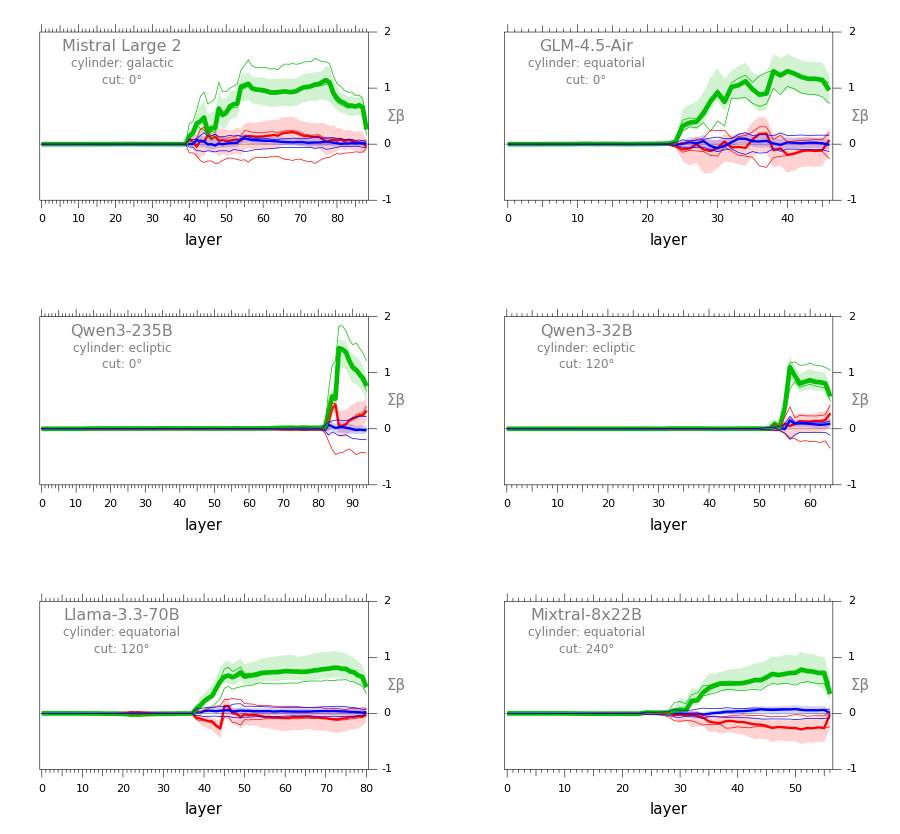
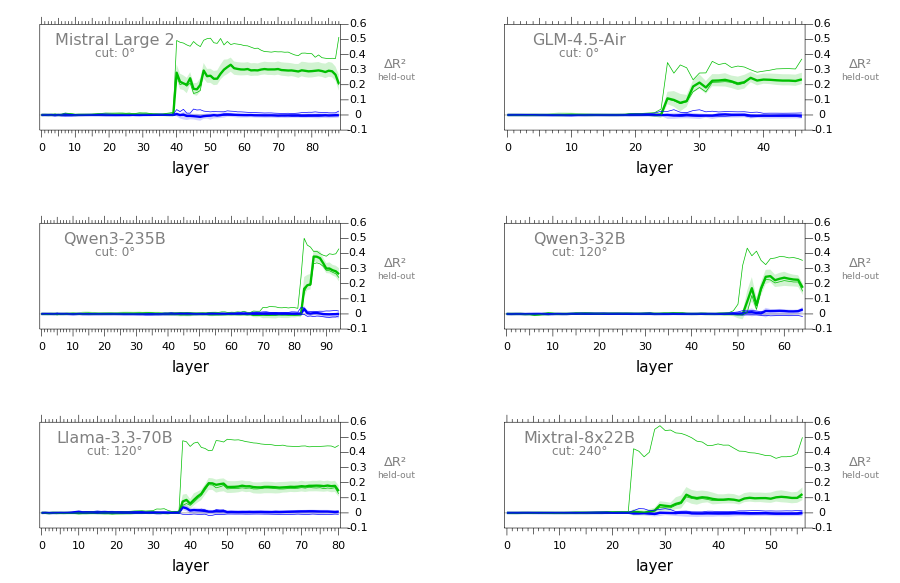
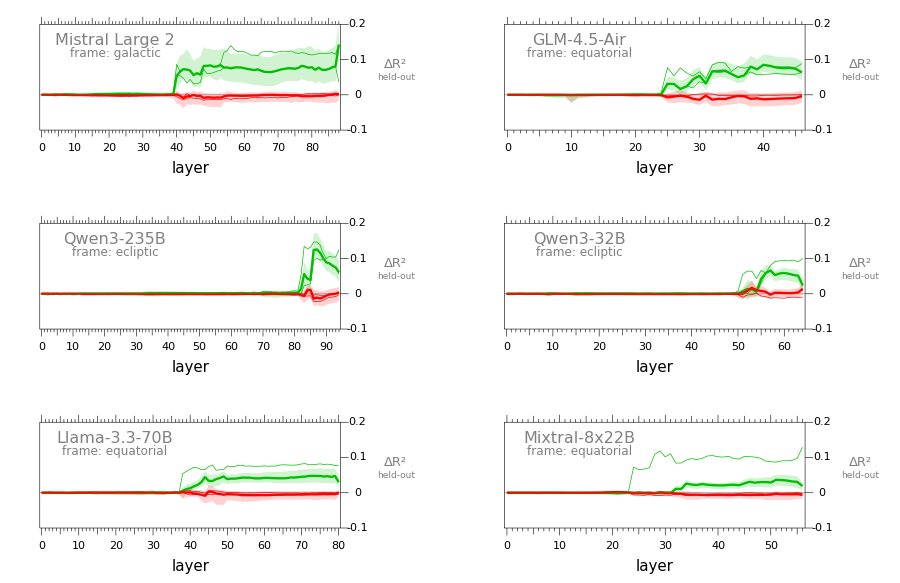
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
(* ====Figures 8 and 19:sphere vs cylinder vs flat chart,three separate figures====*)(*All three from one run:188 objects (85 stars,15 other,88 constellations as points at their area centroids);per split/resample,per-feature standardization,centring of each type on its own mean and the top-8 PCA are fitted in the full hidden space on the training (or drawn) rows (rebuttal/metric_fullpca_cent.py on the raw activations);one RA cut and one cylinder frame per model,chosen by the all-layer mean held-out R^2 of the rival alone (printed in each panel;rebuttal/metric_fullpca_allscore.py+metric_gain_typed.py).vs_original_choice_full.pdf:the paper's OLS on the squared-distance RDM,design sphere (x,y,z)+chart (lat,lon-cut)+cylinder (sin lat,cos lon,sin lon) (=the paper's seven coordinates at cut 0,equatorial);
green thick:sphere (y,z),red:cylinder (cos lon,sin lon),blue:chart (lon-cut).Band:5-95% over 100 object-bootstrap resamples within type,everything refitted per resample (metric_fullpca_score.py--ols-only).vs_chart_linmap_full.pdf/vs_cylinder_linmap_full.pdf:held-out R^2 gain from adding one map's coordinates to the other's,ridge linear map coordinates->8 PCs (cross terms included).Solid+band:median and 5-95% over 100 object splits (20% of each type held out;scored on pairs with a test object).Green:sphere added to the rival;blue/red:chart/cylinder added to the sphere.Thin lines (vsEnvelope=True):sensitivity to the coordinate choice,the lowest and highest value at each layer over all choices (OLS:3 chart frames x 12 cuts x 3 cylinder frames;linmap:chart 3 frames x 12 cuts,cylinder 3 frames;median over splits per choice).Per-model PDFs: <model>_vs_original_choice_full.pdf, <model>_vs_chart_linmap_full.pdf, <model>_vs_cylinder_linmap_full.pdf*)vsModels=Range[6];vsEnvelope=True;
vsW=3;vsTh=0.004;vsGreen=RGBColor[0,0.75,0];vsRed=RGBColor[1,0,0];vsBlue=RGBColor[0,0,1];
vsX[l_][la_]:=vsW*((la-0.5)/l);
vsFrame[l_,ylo_,yhi_]:={Black,Thickness[0.001],Line[{{0,ylo},{vsW,ylo},{vsW,yhi},{0,yhi},{0,ylo}}],Table[With[{h=Which[Mod[i,10]==0,0.07,Mod[i,5]==0,0.06,True,0.03]},{Line[{{vsX[l][i+1],ylo},{vsX[l][i+1],ylo-h}}],Line[{{vsX[l][i+1],yhi},{vsX[l][i+1],yhi+h}}]}],{i,0,l-1}],Table[Text[10*i,{vsX[l][10*i+1],ylo-0.17}],{i,0,Floor[(l-1)/10]}],Text[Style["layer",15],{vsW/2,ylo-0.36}]};
vsYTicks[ticks_]:={Black,Thickness[0.001],Table[{Line[{{vsW,t[[1]]},{vsW+0.08,t[[1]]}}],Text[t[[2]],{vsW+0.17,t[[1]]}]},{t,ticks}]};
(*one curve:{color,thickness,layers (1-based),values,lo,hi},values already in plot units*)
vsCurve[{c_,th_,ls_,v_,lo_,hi_},l_,{ylo_,yhi_}]:=Module[{cl=Clip[#,{ylo,yhi}]&},{{EdgeForm[],c,Opacity[bandOpacity],Polygon[Join[Transpose[{vsX[l]/@ls,cl/@lo}],Reverse[Transpose[{vsX[l]/@ls,cl/@hi}]]]]},{c,Thickness[th],Line[Transpose[{vsX[l]/@ls,cl/@v}]]}}];
vsCutNote[cuts_]:=If[Length[Union[cuts]]==1,"cut: "<>ToString[First[cuts]]<>"°","cut: per layer"];
(*panel notes,top left:model,then the coordinate choices;y in plot units*)
vsNotes[i_,lines_,{y0_,dy_}]:={Text[Style[mmodels[[i]],16],{vsW/4,y0}],Table[Text[Style[lines[[k]],12],{vsW/4,y0-k*dy}],{k,Length[lines]}]};

(*OLS weights (Sum beta) on[sMin,sMax];plotted at half scale as in the paper,tick labels in Sum beta*)
vsOls[i_,{sMin_,sMax_}]:=Module[{T=readCSV["vs/"<>models[[i]]<>"_vs_choice_full.csv"],l,ls,s,lo=sMin/2,hi=sMax/2},l=Length[T];ls=(#["layer"]+1)&/@T;
s[k_]:=Table[(#[k<>suf]/2)&/@T,{suf,{"","_p05","_p95"}}];
Graphics[{GrayLevel[0.5],Thickness[0.001],Line[{{0,0},{vsW,0}}],vsCurve[{vsRed,vsTh,ls,Sequence@@s["cylinder"]},l,{lo,hi}],vsCurve[{vsBlue,vsTh,ls,Sequence@@s["chart"]},l,{lo,hi}],vsCurve[{vsGreen,2*vsTh,ls,Sequence@@s["sphere"]},l,{lo,hi}],If[vsEnvelope,Table[{kc[[2]],Thickness[0.0012],Line[Transpose[{vsX[l]/@ls,Clip[#[kc[[1]]<>e]/2,{lo,hi}]&/@T}]]},{kc,{{"sphere",vsGreen},{"cylinder",vsRed},{"chart",vsBlue}}},{e,{"_envmin","_envmax"}}],{}],vsFrame[l,lo,hi],vsYTicks[{#/2,#}&/@Range[Ceiling[sMin],Floor[sMax]]],Text[Style["Σβ",15],{vsW+0.25,(lo+hi)/2}],vsNotes[i,{"cylinder: "<>First[T]["frame"],vsCutNote[#["cut"]&/@T]},{hi-0.13,0.15}]},ImageSize->420]];

(*held-out linmap gains,mapped from[gmin,gmax] onto[0,1];kind="chart"|"cylinder"*)
vsLin[i_,kind_,c_,{gmin_,gmax_},gTicks_]:=Module[{G=readCSV["vs/"<>models[[i]]<>"_linmap_"<>kind<>"_full.csv"],l,ls,gy,s},gy[g_]:=(g-gmin)/(gmax-gmin);
l=Length[G];ls=(#["layer"]+1)&/@G;
s[k_]:=Table[gy[#[k<>suf]]&/@G,{suf,{"","_p05","_p95"}}];
Graphics[{GrayLevel[0.5],Thickness[0.001],Line[{{0,gy[0]},{vsW,gy[0]}}],vsCurve[{vsGreen,vsTh,ls,Sequence@@s["sphere_to_"<>kind]},l,{0,1}],vsCurve[{c,vsTh,ls,Sequence@@s[kind<>"_to_sphere"]},l,{0,1}],If[vsEnvelope,Table[{kc[[2]],Thickness[0.0012],Line[Transpose[{vsX[l]/@ls,Clip[gy[#[kc[[1]]<>e]],{0,1}]&/@G}]]},{kc,{{"sphere_to_"<>kind,vsGreen},{kind<>"_to_sphere",c}}},{e,{"_envmin","_envmax"}}],{}],vsFrame[l,0,1],vsYTicks[{gy[#],#}&/@gTicks],Text[Style[Row[{"Δ",Superscript["R",2]}],13],{vsW+0.55,0.62}],Text[Style["held-out",9],{vsW+0.55,0.5}],vsNotes[i,{If[kind=="cylinder","frame: "<>First[G]["choice"],vsCutNote[#["choice"]&/@G]]},{0.85,0.13}]},ImageSize->420]];
(*legend items {label,color,style},style "thin"=thin line*)
vsLegend[items_]:=Graphics[Table[{items[[j,2]],Thickness[If[items[[j,3]]==="thin",0.0012,0.004]],Line[{{2.1*(j-1),0},{2.1*(j-1)+0.3,0}}],Black,Text[Style[items[[j,1]],11],{2.1*(j-1)+0.4,0},{-1,0}]},{j,Length[items]}],ImageSize->950,AspectRatio->0.035];
vsGrid[panels_,legend_]:=Column[{legend,GraphicsGrid[Partition[panels,2,2,1,{}],ImageSize->900]},Alignment->Center];

vsFigs=<|"original_choice_full"->{vsOls[#,{-1,2}]&/@vsModels,vsLegend[{}(*{{"sphere (y, z)",vsGreen,False},{"cylinder (cos lon, sin lon)",vsRed,False},{"flat chart (lon - cut)",vsBlue,False}}~Join~If[vsEnvelope,{{"range over frames, cuts",GrayLevel[0.3],"thin"}},{}]*)]},"chart_linmap_full"->{vsLin[#,"chart",vsBlue,{-0.1,0.6},{-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6}]&/@vsModels,vsLegend[{}(*{{"sphere added to chart",vsGreen,False},{"chart added to sphere",vsBlue,False}}~Join~If[vsEnvelope,{{"range over frames, cuts",GrayLevel[0.3],"thin"}},{}]*)]},"cylinder_linmap_full"->{vsLin[#,"cylinder",vsRed,{-0.1,0.2},{-0.1,0,0.1,0.2}]&/@vsModels,vsLegend[{}(*{{"sphere added to cylinder",vsGreen,False},{"cylinder added to sphere",vsRed,False}}~Join~If[vsEnvelope,{{"range over frames",GrayLevel[0.3],"thin"}},{}]*)]}|>;
(*KeyValueMap[Function[{name,f},Export[FileNameJoin[{out,"vs_"<>name<>".pdf"}],vsGrid@@f];
MapThread[Export[FileNameJoin[{out,models[[#1]]<>"_vs_"<>name<>".pdf"}],#2]&,{vsModels,f[[1]]}]],vsFigs];*)
Column[vsGrid@@#&/@Values[vsFigs],Spacings->3]
```

## Q_text saturation with corpus size (Issue 3)

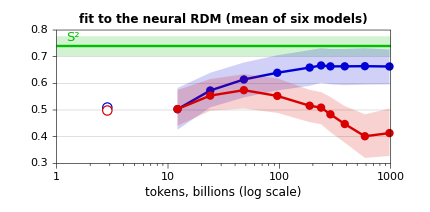

```mathematica
(* x: tokens of the corpus stage (log scale). Stages are nested: the pilot web sample (C4 + FineWeb) in
   prefixes of 1/16 ... 1 (12-187 B tokens), then the whole pilot web plus a growing prefix of the extended
   FineWeb parts (237-975 B); open circles: Wikipedia alone (2.85 B, the paper's corpus). Gated counts,
   positive eigenvalues, all modes (satTop10 = True adds the top-10-mode versions, dashed).
   Blue: baseline from the object-object table, observed diagonal (Figure 10's 975B column);
   red: M* as in appendix F.3, zero diagonal (the published Q_text).
   Left: fit, Pearson r of the Q_text RDM with the neural RDM on constellation pairs, mean over the six strong
   models, on Figure 10's footing (full standardized residual stream); band: 95% over constellation resamples; green: the sphere S^2 on the same footing.
   Right: split-half reliability, Pearson r between the Q_text RDMs of the two halves of each stage (even / odd
   count files, i.e. each half has half the tokens); satSB = True plots the Spearman-Brown estimate 2r/(1+r)
   for the full stage instead. Data: rebuttal/cooc/qtext_saturation.py -> data/rdm/qtext_saturation.csv *)
SAT = readCSV["rdm/qtext_saturation.csv"];
satCons = {{"within", RGBColor[0, 0, 0.85], "baseline from the object-object table (Fig. 10: 975B)"},
   {"faithful", RGBColor[0.85, 0, 0], "M* as in appendix F.3 (published)"}};
satTop10 = False; satSB = False;
satW = 2.5; satT = {1, 1000};
satX[t_] := satW*Log10[t/satT[[1]]]/Log10[satT[[2]]/satT[[1]]];
satSer[c_, ser_] := SortBy[Select[SAT, #construction === c && #series === ser &], #["tokens_B"] &];
satSph = row1[SAT, #construction === "sphere" &];
satPanel[key_, {lo_, hi_}, step_, title_, ref_] := Module[{gy, cons},
   gy[v_] := (Clip[v, {lo, hi}] - lo)/(hi - lo);
   cons = If[satTop10, Join[satCons, {#[[1]] <> "_top10", #[[2]], #[[3]]} & /@ satCons], satCons];
   Graphics[{
     Thickness[0.001], GrayLevel[0.8], Table[Line[{{0, gy[y]}, {satW, gy[y]}}], {y, lo + step, hi - step/2, step}],
     If[ref, {RGBColor[0, 0.75, 0], Opacity[bandOpacity], EdgeForm[], Rectangle[{0, gy[satSph["fit_lo"]]}, {satW, gy[satSph["fit_hi"]]}],
       Opacity[1], Thickness[0.004], Line[{{0, gy[satSph["fit"]]}, {satW, gy[satSph["fit"]]}}],
       Text[Style[Superscript["S", 2], 13], {0.12, gy[satSph["fit"]] + 0.06}]}, {}],
     Table[With[{s = satSer[c[[1]], "nested"], wk = satSer[c[[1]], "wikipedia"], col = c[[2]],
        dash = If[StringEndsQ[c[[1]], "_top10"], Dashing[{0.012, 0.008}], Dashing[None]]},
       {If[key === "fit", {col, Opacity[bandOpacity], EdgeForm[],
          Polygon[Join[{satX[#["tokens_B"]], gy[#["fit_lo"]]} & /@ s, Reverse[{satX[#["tokens_B"]], gy[#["fit_hi"]]} & /@ s]]]}, {}],
        {col, Opacity[1], dash, Thickness[0.004], Line[{satX[#["tokens_B"]], gy[#[key]]} & /@ s]},
        {col, PointSize[0.014], Point[{satX[#["tokens_B"]], gy[#[key]]} & /@ s]},
        Table[If[NumericQ[r[key]], {White, Disk[{satX[r["tokens_B"]], gy[r[key]]}, 0.035], col, Thickness[0.002],
           Circle[{satX[r["tokens_B"]], gy[r[key]]}, 0.035]}, {}], {r, wk}]}], {c, cons}],
     Black, Thickness[0.001], Line[{{0, 0}, {satW, 0}, {satW, 1}, {0, 1}, {0, 0}}],
     Table[{Line[{{satX[t], 0}, {satX[t], -0.04}}], Text[t, {satX[t], -0.1}]}, {t, {1, 10, 100, 1000}}],
     Table[Line[{{satX[m*10^e], 0}, {satX[m*10^e], -0.02}}], {e, 0, 2}, {m, 2, 9}],
     Table[{Line[{{0, gy[y]}, {-0.03, gy[y]}}], Text[y, {-0.13, gy[y]}]}, {y, lo, hi, step}],
     Text[Style["tokens, billions (log scale)", 12], {satW/2, -0.22}], Text[Style[title, Bold, 12], {satW/2, 1.08}]},
    ImageSize -> 430]];
satLegend = Graphics[Table[{satCons[[j, 2]], Thickness[0.004], Line[{{3.3*(j - 1), 0}, {3.3*(j - 1) + 0.3, 0}}],
      Black, Text[Style[satCons[[j, 3]], 11], {3.3*(j - 1) + 0.4, 0}, {-1, 0}]}, {j, Length[satCons]}]~Join~
     {{Black, Text[Style["○", 15], {6.85, 0}], Text[Style["Wikipedia alone", 11], {6.95, 0}, {-1, 0}]},
      {RGBColor[0, 0.75, 0], Thickness[0.004], Line[{{8.6, 0}, {8.9, 0}}], Black, Text[Style[Row[{"sphere ", Superscript["S", 2]}], 11], {9.0, 0}, {-1, 0}]}},
   ImageSize -> 900, AspectRatio -> 0.03];
figSat = Column[{GraphicsRow[{satPanel["fit", {0.3, 0.8}, 0.1, "fit to the neural RDM (mean of six models)", True](*,
      satPanel[If[satSB, "spearman_brown", "split_half"], {0, 1}, 0.1, If[satSB, "reliability (Spearman-Brown)", "split-half reliability"], False]*)}, ImageSize -> 400](*,
    satLegend*)}, Alignment -> Center];
Export[FileNameJoin[{out, "qtext_saturation.pdf"}], figSat];
figSat
```